```mathematica
SetDirectory[NotebookDirectory[]]
Import["GraphPartition.m"]
<< GraphPartition`
$Context
```

C:\Users\Chuqian\Desktop\research\graphPartitioning

Global`

```mathematica
RandomGrid1[m_,n_,maxDist_:1, maxFanOut_:4]:= Module[{elist={},
vlist = Range[1,m*n],
vcoords= Flatten[Table[{i,j},{i,1,m},{j,1,n}],1],
 newE, neighbor},

Vertex1D[ij_] := (First[ij]-1)*n+Last[ij];
Neighbors[i_,j_,dist_] := Select[Flatten[Table[{i+di, j+dj},{di,-dist,dist},{dj,-dist,dist}],1],
1<=First[#]≤m && 1≤Last[#]≤n && #≠{i,j}&];
elist={};
Do[AppendTo[elist,{Vertex1D[{i,j}],Vertex1D[neighbor]}],
{i,1,m},{j,1,n},{neighbor, RandomChoice[Neighbors[i,j,maxDist],(*RandomInteger[{1,*)maxFanOut(*}]*)]}]
elist =DeleteDuplicates[elist,#1==#2||#1==Reverse[#2]& ];
(*Make sure that the result graph is connected*)
With[{components=#[[1]]&/@ConnectedComponents[elist]},
If[Length[components]>1,
elist=Join[elist, Map[{components[[1]], #}&,components[[2;;]]]];,
Nothing]];
newG=System`Graph[vlist,elist,VertexCoordinates->vcoords,
System`VertexWeight->Table[1/Length[vlist], Length[vlist]],System`EdgeWeight-> Table[1,Length[elist]],
System`VertexLabels->If[Max[m,n]<5,Automatic, None],
System`EdgeStyle->Directive[Opacity[0.5], Thick](*, EdgeShapeFunction->"Arrow"*)];
newG (*UndirectedGraph[newG]*)]
(*g=RandomGrid1[12,12, maxDist=2, maxFanOut=2]*)
```

Set::write: Tag Times in Null {{1,3},{1,2},{2,26},{2,14},{3,2},{3,1},{4,28},{4,15},{5,27},{5,16},{6,32},{6,30},{7,5},{7,18},{8,22},{8,7},{9,20},{9,22},{10,24},{10,21},{11,12},{11,12},{12,24},{12,35},{13,26},{13,1},{14,2},{14,13},{15,39},{15,38},{16,38},{16,28},{17,28},{17,39},{18,17},{18,31},{19,5},{19,44},{20,6},{20,6},{21,22},{21,47},{22,24},{22,24},{23,48},{23,45},{24,34},{24,47},{25,38},{25,15},«238»} is Protected.

-Graphics-

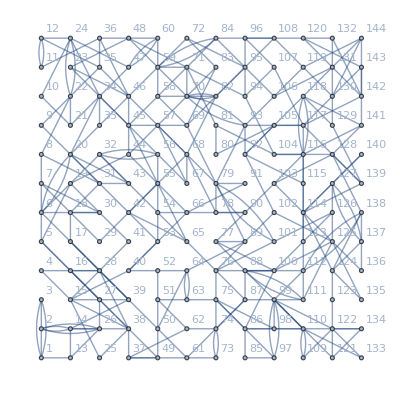

Set::write: Tag Times in Null {{1,13},{1,39},{2,1},{2,41},{3,42},{3,41},{4,17},{4,5},{5,6},{5,30},{6,3},{6,30},{7,9},{7,4},{8,42},{8,23},{9,7},{9,35},{10,43},{10,24},{11,22},{11,45},{12,21},{12,11},{13,14},{13,50},{14,51},{14,37},{15,16},{15,27},{16,40},{16,52},{17,56},{17,14},{18,41},{18,15},{19,32},{19,30},{20,43},{20,58},{21,35},{21,47},{22,19},{22,24},{23,8},{23,59},{24,57},{24,58},{25,38},{25,39},«238»} is Protected.

Set::write: Tag Times in Null\\\ {{1, 22}, {1, 12}, {2, 12}, {2, 14}, {3, 15}, {3, 23}, {4, 25}, {4, 2}, {5, 17}, {5, 25}, {6, 24}, {6, 18}, {7, 26}, {7, 29}, {8, 20}, {8, 18}, {9, 19}, {9, 10}, {10, 18}, {10, 8}, {11, 33}, {11, 23}, {12, 2}, {12, 3}, {13, 15}, {13, 35}, {14, 6}, {14, 13}, {15, 26}, {15, 26}, {16, 4}, {16, 35}, {17, 9}, {17, 28}, {18, 29}, {18, 8}, {19, 8}, {19, 39}, {20, 30}, {20, 28}, {21, 42}, {21, 42}, {22, 3}, {22, 1}, {23, 42}, {23, 13}, {24, 5}, {24, 42}, {25, 27}, {25, 36}, «150»} is Protected.

-Graphics-

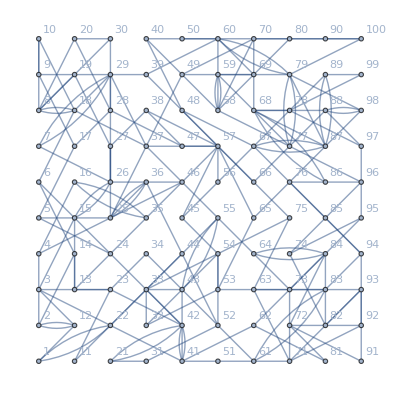

```mathematica
sym=LineGraph[GridGraph[{5,5}]];
g =RandomGrid1[12,12, maxDist=3, maxFanOut=2]
(*g = EdgeDelete[sym,EdgeList[sym][[RandomSample[Range[Length[EdgeList[sym]]],8]]]]*)
g=UndirectedGraph[#,VertexLabels->Automatic,VertexWeight->Table[1/V[#],V[#]], EdgeWeight->Automatic]&@g
```

```mathematica
Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->2, IncludeObj->True,GroundingScheme->GroundingRandom]][[1]],100]]

Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->2, IncludeObj->True,GroundingScheme->GroundingPreviousMax]][[1]],100]]
Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->2, IncludeObj->True,GroundingScheme->GroundingPreviousMedian]][[1]],100]]
Mean[
Table[
N[MultipleIsoperimetricEdges[g,NumBasis->2, IncludeObj->True,GroundingScheme->(GroundingSubset[#1,#2,Ratio->5]&)]][[1]],100]]
Mean[
Table[N[MultipleIsoperimetricEdges[g,NumBasis->2, IncludeObj->True,GroundingScheme->GroundingMaxDegree]][[1]],100]]
N[SpectralEdges[g,IncludeObj->True]]
```

89.4177

117.158

86.6516

119.253

153.061

Less::nord: Invalid comparison with 6.26612+0.0824946 ⅈ attempted.

Less::nord: Invalid comparison with 5.7208+0.106178 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{426.136,{6.<->18.,8.<->20.,9.<->19.,9.<->10.,10.<->18.,10.<->8.,11.<->33.,11.<->23.,17.<->9.,18.<->29.,19.<->8.,19.<->39.,25.<->27.,26.<->27.,26.<->46.,27.<->19.,27.<->38.,30.<->8.,31.<->52.,32.<->54.,32.<->53.,33.<->32.,34.<->52.,37.<->18.,39.<->57.,39.<->60.,46.<->37.,46.<->25.,49.<->70.,50.<->70.,52.<->54.,52.<->44.,61.<->52.,64.<->46.,70.<->68.,70.<->58.,76.<->98.,80.<->70.,88.<->98.,90.<->70.,95.<->97.,97.<->78.,97.<->88.,98.<->79.,98.<->88.}}

```mathematica
Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->3, IncludeObj->True,GroundingScheme->GroundingRandom]][[1]],100]]

Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->3, IncludeObj->True,GroundingScheme->GroundingPreviousMax]][[1]],100]]
Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->3, IncludeObj->True,GroundingScheme->GroundingPreviousMedian]][[1]],100]]
Mean[
Table[
N[MultipleIsoperimetricEdges[g,NumBasis->3, IncludeObj->True,GroundingScheme->(GroundingSubset[#1,#2,Ratio->5]&)]][[1]],100]]
Mean[
Table[N[MultipleIsoperimetricEdges[g,NumBasis->3, IncludeObj->True,GroundingScheme->GroundingMaxDegree]][[1]],100]]
N[SpectralEdges[g,IncludeObj->True]]
```

77.9614

62.0043

65.4109

112.856

51.4259

Less::nord: Invalid comparison with 6.26612+0.0824946 ⅈ attempted.

Less::nord: Invalid comparison with 5.7208+0.106178 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{426.136,{6.<->18.,8.<->20.,9.<->19.,9.<->10.,10.<->18.,10.<->8.,11.<->33.,11.<->23.,17.<->9.,18.<->29.,19.<->8.,19.<->39.,25.<->27.,26.<->27.,26.<->46.,27.<->19.,27.<->38.,30.<->8.,31.<->52.,32.<->54.,32.<->53.,33.<->32.,34.<->52.,37.<->18.,39.<->57.,39.<->60.,46.<->37.,46.<->25.,49.<->70.,50.<->70.,52.<->54.,52.<->44.,61.<->52.,64.<->46.,70.<->68.,70.<->58.,76.<->98.,80.<->70.,88.<->98.,90.<->70.,95.<->97.,97.<->78.,97.<->88.,98.<->79.,98.<->88.}}

```mathematica
Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->5, IncludeObj->True,GroundingScheme->GroundingRandom]][[1]],100]]

Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->5, IncludeObj->True,GroundingScheme->GroundingPreviousMax]][[1]],100]]
Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->5, IncludeObj->True,GroundingScheme->GroundingPreviousMedian]][[1]],100]]
Mean[
Table[
N[MultipleIsoperimetricEdges[g,NumBasis->5, IncludeObj->True,GroundingScheme->(GroundingSubset[#1,#2,Ratio->5]&)]][[1]],100]]
Mean[
Table[N[MultipleIsoperimetricEdges[g,NumBasis->5, IncludeObj->True,GroundingScheme->GroundingMaxDegree]][[1]],100]]
N[SpectralEdges[g,IncludeObj->True]]
```

60.7923

71.457

55.1973

99.5386

53.424

Less::nord: Invalid comparison with 6.26612+0.0824946 ⅈ attempted.

Less::nord: Invalid comparison with 5.7208+0.106178 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{426.136,{6.<->18.,8.<->20.,9.<->19.,9.<->10.,10.<->18.,10.<->8.,11.<->33.,11.<->23.,17.<->9.,18.<->29.,19.<->8.,19.<->39.,25.<->27.,26.<->27.,26.<->46.,27.<->19.,27.<->38.,30.<->8.,31.<->52.,32.<->54.,32.<->53.,33.<->32.,34.<->52.,37.<->18.,39.<->57.,39.<->60.,46.<->37.,46.<->25.,49.<->70.,50.<->70.,52.<->54.,52.<->44.,61.<->52.,64.<->46.,70.<->68.,70.<->58.,76.<->98.,80.<->70.,88.<->98.,90.<->70.,95.<->97.,97.<->78.,97.<->88.,98.<->79.,98.<->88.}}

```mathematica
Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->10, IncludeObj->True,GroundingScheme->GroundingRandom]][[1]],100]]

Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->10, IncludeObj->True,GroundingScheme->GroundingPreviousMax]][[1]],100]]
Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->10, IncludeObj->True,GroundingScheme->GroundingPreviousMedian]][[1]],100]]
Mean[
Table[
N[MultipleIsoperimetricEdges[g,NumBasis->10, IncludeObj->True,GroundingScheme->(GroundingSubset[#1,#2,Ratio->5]&)]][[1]],100]]
Mean[
Table[N[MultipleIsoperimetricEdges[g,NumBasis->10, IncludeObj->True,GroundingScheme->GroundingMaxDegree]][[1]],100]]
N[SpectralEdges[g,IncludeObj->True]]
```

59.0102

76.7334

59.0254

79.8045

53.424

Less::nord: Invalid comparison with 6.26612+0.0824946 ⅈ attempted.

Less::nord: Invalid comparison with 5.7208+0.106178 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{426.136,{6.<->18.,8.<->20.,9.<->19.,9.<->10.,10.<->18.,10.<->8.,11.<->33.,11.<->23.,17.<->9.,18.<->29.,19.<->8.,19.<->39.,25.<->27.,26.<->27.,26.<->46.,27.<->19.,27.<->38.,30.<->8.,31.<->52.,32.<->54.,32.<->53.,33.<->32.,34.<->52.,37.<->18.,39.<->57.,39.<->60.,46.<->37.,46.<->25.,49.<->70.,50.<->70.,52.<->54.,52.<->44.,61.<->52.,64.<->46.,70.<->68.,70.<->58.,76.<->98.,80.<->70.,88.<->98.,90.<->70.,95.<->97.,97.<->78.,97.<->88.,98.<->79.,98.<->88.}}

```mathematica
Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->15, IncludeObj->True,GroundingScheme->GroundingRandom]][[1]],100]]

Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->15, IncludeObj->True,GroundingScheme->GroundingPreviousMax]][[1]],100]]
Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->15, IncludeObj->True,GroundingScheme->GroundingPreviousMedian]][[1]],100]]
Mean[
Table[
N[MultipleIsoperimetricEdges[g,NumBasis->15, IncludeObj->True,GroundingScheme->(GroundingSubset[#1,#2,Ratio->5]&)]][[1]],100]]
Mean[
Table[N[MultipleIsoperimetricEdges[g,NumBasis->15, IncludeObj->True,GroundingScheme->GroundingMaxDegree]][[1]],100]]
N[SpectralEdges[g,IncludeObj->True]]
```

57.3824

75.6236

59.1866

74.187

57.1429

Less::nord: Invalid comparison with 6.26612+0.0824946 ⅈ attempted.

Less::nord: Invalid comparison with 5.7208+0.106178 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{426.136,{6.<->18.,8.<->20.,9.<->19.,9.<->10.,10.<->18.,10.<->8.,11.<->33.,11.<->23.,17.<->9.,18.<->29.,19.<->8.,19.<->39.,25.<->27.,26.<->27.,26.<->46.,27.<->19.,27.<->38.,30.<->8.,31.<->52.,32.<->54.,32.<->53.,33.<->32.,34.<->52.,37.<->18.,39.<->57.,39.<->60.,46.<->37.,46.<->25.,49.<->70.,50.<->70.,52.<->54.,52.<->44.,61.<->52.,64.<->46.,70.<->68.,70.<->58.,76.<->98.,80.<->70.,88.<->98.,90.<->70.,95.<->97.,97.<->78.,97.<->88.,98.<->79.,98.<->88.}}

```mathematica
Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->20, IncludeObj->True,GroundingScheme->GroundingRandom]][[1]],100]]

Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->20, IncludeObj->True,GroundingScheme->GroundingPreviousMax]][[1]],100]]
Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->20, IncludeObj->True,GroundingScheme->GroundingPreviousMedian]][[1]],100]]
Mean[
Table[
N[MultipleIsoperimetricEdges[g,NumBasis->20, IncludeObj->True,GroundingScheme->(GroundingSubset[#1,#2,Ratio->3]&)]][[1]],100]]
Mean[
Table[N[MultipleIsoperimetricEdges[g,NumBasis->20, IncludeObj->True,GroundingScheme->GroundingMaxDegree]][[1]],100]]
N[SpectralEdges[g,IncludeObj->True]]
```

150.325

148.568

149.546

152.921

176.636

Less::nord: Invalid comparison with 2.28927+0.00432532 ⅈ attempted.

Less::nord: Invalid comparison with 2.28927-0.00432532 ⅈ attempted.

Less::nord: Invalid comparison with 2.28927+0.00432532 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{134.31,{5.<->3.,10.<->25.,33.<->77.,46.<->74.,46.<->17.,49.<->88.,52.<->10.,53.<->31.,77.<->25.,78.<->72.,94.<->2.}}

#### Spanners

Set::write: Tag Times in Null {{1,26},{1,59},{2,74},{2,47},{3,9},{3,55},{4,95},{4,12},{5,3},{5,10},{6,74},{6,97},{7,26},{7,72},{8,70},{8,42},{9,65},{9,19},{10,49},{10,25},{11,28},{11,70},{12,73},{12,16},{13,84},{«1»},{14,10},{14,46},{15,48},{15,58},{16,9},{16,47},{17,85},{17,91},{18,59},{18,85},{19,47},{19,82},{20,28},{20,12},{21,45},{21,43},{22,3},{22,37},{23,31},{23,83},{24,52},{24,56},{25,96},{25,47},«150»} is Protected.

-Graphics-

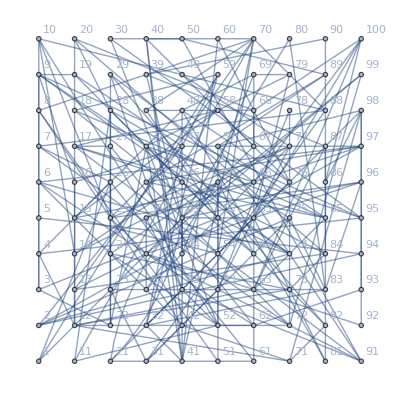

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
sym=LineGraph[GridGraph[{5,5}]];
g =RandomGrid1[10,10, maxDist=10, maxFanOut=2]
(*g = EdgeDelete[sym,EdgeList[sym][[RandomSample[Range[Length[EdgeList[sym]]],8]]]]*)
g=UndirectedGraph[#,VertexLabels->Automatic,VertexWeight->Table[1/V[#],V[#]], EdgeWeight->Automatic]&@g
```

```mathematica
Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->2, IncludeObj->True,GroundingScheme->GroundingRandom]][[1]],100]]

Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->2, IncludeObj->True,GroundingScheme->GroundingPreviousMax]][[1]],100]]
Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->2, IncludeObj->True,GroundingScheme->GroundingPreviousMedian]][[1]],100]]
Mean[
Table[
N[MultipleIsoperimetricEdges[g,NumBasis->2, IncludeObj->True,GroundingScheme->(GroundingSubset[#1,#2,Ratio->5]&)]][[1]],100]]
Mean[
Table[N[MultipleIsoperimetricEdges[g,NumBasis->2, IncludeObj->True,GroundingScheme->GroundingMaxDegree]][[1]],100]]
N[SpectralEdges[g,IncludeObj->True]]
```

159.205

171.236

159.988

163.603

138.667

Less::nord: Invalid comparison with 2.28927+0.00432532 ⅈ attempted.

Less::nord: Invalid comparison with 2.28927-0.00432532 ⅈ attempted.

Less::nord: Invalid comparison with 2.28927+0.00432532 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{134.31,{5.<->3.,10.<->25.,33.<->77.,46.<->74.,46.<->17.,49.<->88.,52.<->10.,53.<->31.,77.<->25.,78.<->72.,94.<->2.}}

```mathematica
Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->3, IncludeObj->True,GroundingScheme->GroundingRandom]][[1]],100]]

Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->3, IncludeObj->True,GroundingScheme->GroundingPreviousMax]][[1]],100]]
Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->3, IncludeObj->True,GroundingScheme->GroundingPreviousMedian]][[1]],100]]
Mean[
Table[
N[MultipleIsoperimetricEdges[g,NumBasis->3, IncludeObj->True,GroundingScheme->(GroundingSubset[#1,#2,Ratio->5]&)]][[1]],100]]
Mean[
Table[N[MultipleIsoperimetricEdges[g,NumBasis->3, IncludeObj->True,GroundingScheme->GroundingMaxDegree]][[1]],100]]
N[SpectralEdges[g,IncludeObj->True]]
```

164.65

168.942

162.299

166.438

139.86

Less::nord: Invalid comparison with 2.28927+0.00432532 ⅈ attempted.

Less::nord: Invalid comparison with 2.28927-0.00432532 ⅈ attempted.

Less::nord: Invalid comparison with 2.28927+0.00432532 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{134.31,{5.<->3.,10.<->25.,33.<->77.,46.<->74.,46.<->17.,49.<->88.,52.<->10.,53.<->31.,77.<->25.,78.<->72.,94.<->2.}}

```mathematica
Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->5, IncludeObj->True,GroundingScheme->GroundingRandom]][[1]],100]]

Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->5, IncludeObj->True,GroundingScheme->GroundingPreviousMax]][[1]],100]]
Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->5, IncludeObj->True,GroundingScheme->GroundingPreviousMedian]][[1]],100]]
Mean[
Table[
N[MultipleIsoperimetricEdges[g,NumBasis->5, IncludeObj->True,GroundingScheme->(GroundingSubset[#1,#2,Ratio->5]&)]][[1]],100]]
Mean[
Table[N[MultipleIsoperimetricEdges[g,NumBasis->5, IncludeObj->True,GroundingScheme->GroundingMaxDegree]][[1]],100]]
N[SpectralEdges[g,IncludeObj->True]]
```

158.194

165.428

158.75

160.925

156.25

Less::nord: Invalid comparison with 2.28927+0.00432532 ⅈ attempted.

Less::nord: Invalid comparison with 2.28927-0.00432532 ⅈ attempted.

Less::nord: Invalid comparison with 2.28927+0.00432532 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{134.31,{5.<->3.,10.<->25.,33.<->77.,46.<->74.,46.<->17.,49.<->88.,52.<->10.,53.<->31.,77.<->25.,78.<->72.,94.<->2.}}

```mathematica
Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->10, IncludeObj->True,GroundingScheme->GroundingRandom]][[1]],100]]

Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->10, IncludeObj->True,GroundingScheme->GroundingPreviousMax]][[1]],100]]
Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->10, IncludeObj->True,GroundingScheme->GroundingPreviousMedian]][[1]],100]]
Mean[
Table[
N[MultipleIsoperimetricEdges[g,NumBasis->10, IncludeObj->True,GroundingScheme->(GroundingSubset[#1,#2,Ratio->5]&)]][[1]],100]]
Mean[
Table[N[MultipleIsoperimetricEdges[g,NumBasis->10, IncludeObj->True,GroundingScheme->GroundingMaxDegree]][[1]],100]]
N[SpectralEdges[g,IncludeObj->True]]
```

155.121

161.45

155.468

155.71

153.509

Less::nord: Invalid comparison with 2.28927+0.00432532 ⅈ attempted.

Less::nord: Invalid comparison with 2.28927-0.00432532 ⅈ attempted.

Less::nord: Invalid comparison with 2.28927+0.00432532 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{134.31,{5.<->3.,10.<->25.,33.<->77.,46.<->74.,46.<->17.,49.<->88.,52.<->10.,53.<->31.,77.<->25.,78.<->72.,94.<->2.}}

```mathematica
Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->15, IncludeObj->True,GroundingScheme->GroundingRandom]][[1]],100]]

Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->15, IncludeObj->True,GroundingScheme->GroundingPreviousMax]][[1]],100]]
Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->15, IncludeObj->True,GroundingScheme->GroundingPreviousMedian]][[1]],100]]
Mean[
Table[
N[MultipleIsoperimetricEdges[g,NumBasis->15, IncludeObj->True,GroundingScheme->(GroundingSubset[#1,#2,Ratio->5]&)]][[1]],100]]
Mean[
Table[N[MultipleIsoperimetricEdges[g,NumBasis->15, IncludeObj->True,GroundingScheme->GroundingMaxDegree]][[1]],100]]
N[SpectralEdges[g,IncludeObj->True]]
```

149.953

152.841

155.61

152.772

156.25

Less::nord: Invalid comparison with 2.28927+0.00432532 ⅈ attempted.

Less::nord: Invalid comparison with 2.28927-0.00432532 ⅈ attempted.

Less::nord: Invalid comparison with 2.28927+0.00432532 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{134.31,{5.<->3.,10.<->25.,33.<->77.,46.<->74.,46.<->17.,49.<->88.,52.<->10.,53.<->31.,77.<->25.,78.<->72.,94.<->2.}}

```mathematica
Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->20, IncludeObj->True,GroundingScheme->GroundingRandom]][[1]],100]]

Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->20, IncludeObj->True,GroundingScheme->GroundingPreviousMax]][[1]],100]]
Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->20, IncludeObj->True,GroundingScheme->GroundingPreviousMedian]][[1]],100]]
Mean[
Table[
N[MultipleIsoperimetricEdges[g,NumBasis->20, IncludeObj->True,GroundingScheme->(GroundingSubset[#1,#2,Ratio->5]&)]][[1]],100]]
Mean[
Table[N[MultipleIsoperimetricEdges[g,NumBasis->20, IncludeObj->True,GroundingScheme->GroundingMaxDegree]][[1]],100]]
N[SpectralEdges[g,IncludeObj->True]]
```

150.638

149.06

153.061

153.061

176.636

Less::nord: Invalid comparison with 2.28927+0.00432532 ⅈ attempted.

Less::nord: Invalid comparison with 2.28927-0.00432532 ⅈ attempted.

Less::nord: Invalid comparison with 2.28927+0.00432532 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{134.31,{5.<->3.,10.<->25.,33.<->77.,46.<->74.,46.<->17.,49.<->88.,52.<->10.,53.<->31.,77.<->25.,78.<->72.,94.<->2.}}